```mathematica
data=Import["/home/jure/Documents/opengl_ucenje/benchmarks/benchmarks.csv"];
data=Take[data,{11,data//Length}];
headers=Partition[data[[1]],11];
cols=data[[1]];
data=Take[data,{2,data//Length}];
```

```mathematica
benchmarks={"bitonic_2n_float_sort_bench", "bitonic_8n_float_sort_bench","bitonic_float_sort_bench", "std_float_sort_bench"};
cols
```

{bitonic_2n_float_sort_bench/8,1527915,455.195,457.513,ns,,,,,,8}

```mathematica
GetBenchData[name_]:=Block [{tab},
tab=Table[If[(StringPosition[data[[i,1]], name]//Length  && Length[data[[i]]]>5)≠0,data[[i]], ""],{i,1,data//Length}];
tab=DeleteCases[tab, ""];
Return [tab];
];
```

```mathematica
data1=GetBenchData[benchmarks[[1]]];
data1=Take[data1, {1, (data1//Length)-2}];
timing1=data1[[All,4]];
NumToSort1=data1[[All,11]];
```

```mathematica
data2=GetBenchData[benchmarks[[2]]];
data2=Take[data2, {1, (data2//Length)-2}];
timing2=data2[[All,4]];
NumToSort2=data2[[All,11]];
```

```mathematica
data3=GetBenchData[benchmarks[[3]]];
data3=Take[data3, {1, (data3//Length)-2}];
timing3=data3[[All,4]];
NumToSort3=data3[[All,11]];
```

```mathematica
data4=GetBenchData[benchmarks[[4]]];
data4=Take[data4, {1, (data4//Length)-2}];
timing4=data4[[All,4]];
NumToSort4=data4[[All,11]];
```

```mathematica
p1=Transpose[{NumToSort1,timing1}];
p2=Transpose[{NumToSort2,timing2}];
p3=SortBy[Transpose[{NumToSort3,timing3}], First];
p4=SortBy[Transpose[{NumToSort4,timing4}], First];
```

```mathematica
color=ColorData[1,"ColorList"];
LegendFontSize=20;
legenda=
PointLegend[{
{color[[1]],AbsolutePointSize[8]},
{color[[2]],AbsolutePointSize[8]},
{color[[3]],AbsolutePointSize[8]},
{color[[4]], AbsolutePointSize[8]},
Directive[color[[9]], AbsolutePointSize[8]]},
{Style["2^n sort", LegendFontSize], Style["8n sort", LegendFontSize], Style["arbitrary sort", LegendFontSize], 
Style["std sort", LegendFontSize]},
LegendLabel->"", LegendLayout->{"Row",6}];
```

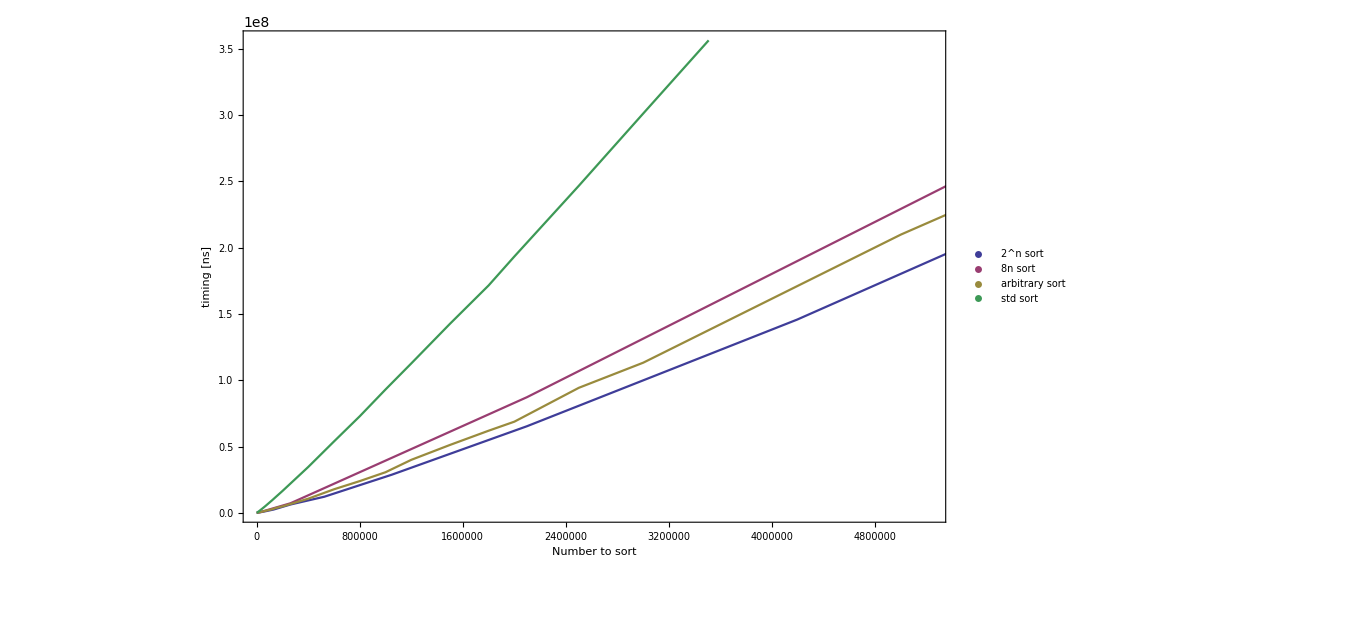

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {1*10^6, 2*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->Automatic,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

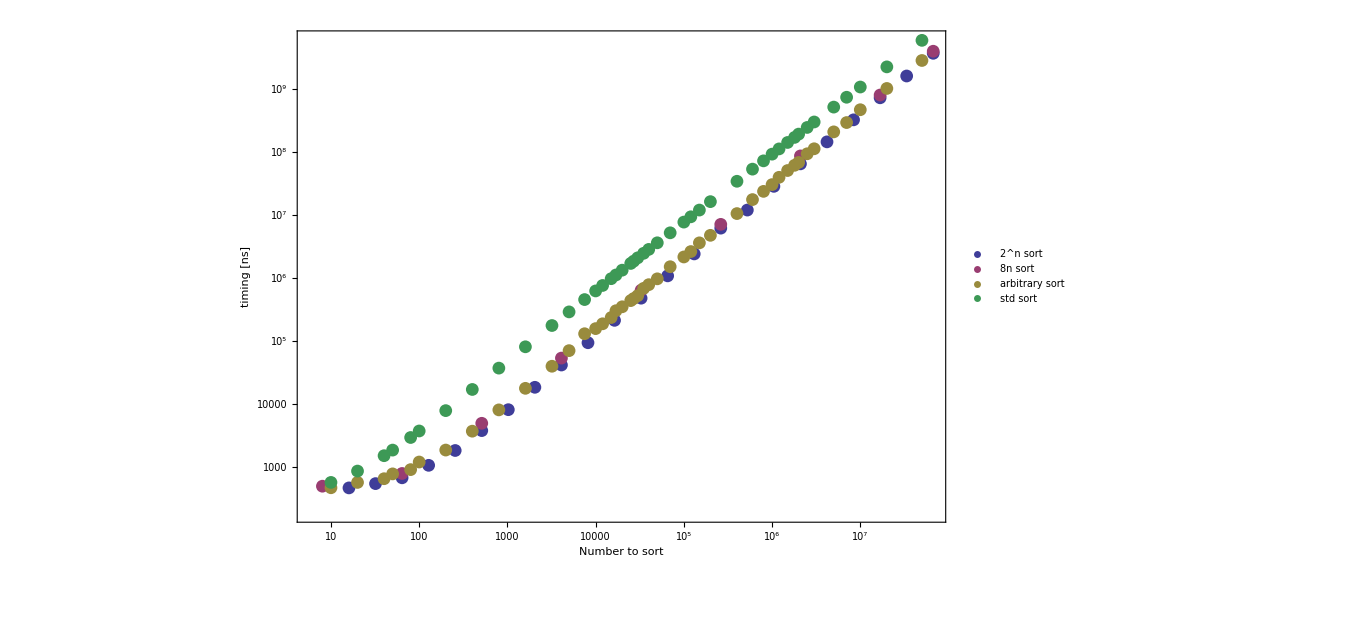

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLogLogPlot[{
p1,p2,p3,p4
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {1*10^6, 2*10^8}],
AxesOrigin->{-100, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->Automatic,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

```mathematica
NonlinearModelFit[Take[p1, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p2, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p3, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p4, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
```

FittedModel[1.53223 x+1.00642×10^-7 x^2+0.144215 x Log[x]^2]

FittedModel[26.4501 x+1.61281×10^-7 x^2+0.0682601 x Log[x]^2]

FittedModel[-18.8238 x-8.08282×10^-8 x^2+0.253911 x Log[x]^2]

FittedModel[55.7312 x-1.07779×10^-8 x^2+0.202265 x Log[x]^2]

```mathematica
(*speedup calculation in comparison to std*)

speedup=Table[{p3[[i,1]],p4[[i,2]]/p3[[i,2]]},{i,1,p3//Length}]
```

{{10,1.21523},{20,1.51352},{40,2.31791},{50,2.38354},{80,3.23106},{100,3.10704},{200,4.22051},{400,4.58791},{800,4.59647},{1600,4.55828},{3200,4.42525},{5000,293023/71186},{7500,229791/65983},{10000,629903/159043},{12000,769126/189731},{15000,492529/119138},{17000,3.68835},{20000,3.80906},{25000,3.88643},{27000,3.91513},{30000,3.98206},{35000,3.59514},{40000,3.62554},{50000,3.72765},{70000,3.4498},{100000,3.57367},{120000,3.56003},{150000,3.31217},{200000,3.42222},{400000,3.25317},{600000,3.03898},{800000,3.04791},{1.×10^6,3.04104},{1.2×10^6,2.82144},{1.5×10^6,2.78635},{1.8×10^6,2.77052},{2.×10^6,2.8134},{2.5×10^6,2.61686},{3.×10^6,2.66053},{5.×10^6,2.47065},{7.×10^6,2.51986},{1.×10^7,2.29125},{2.×10^7,2.19896},{5.×10^7,2.08594}}

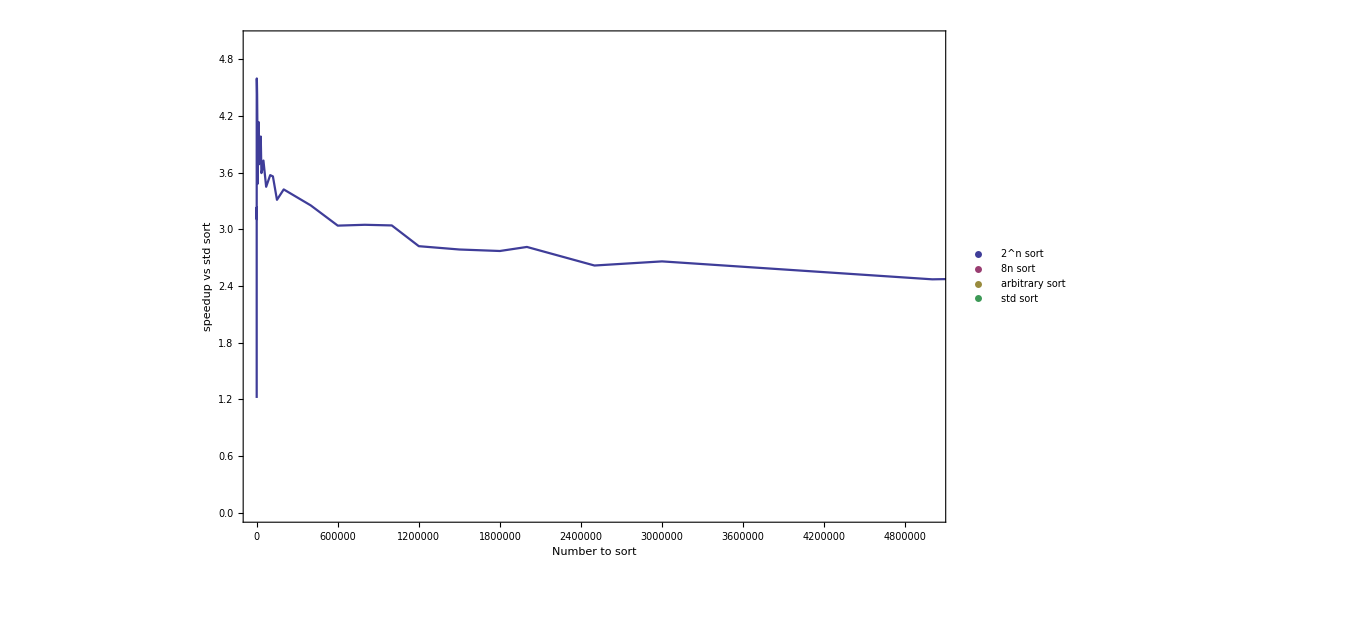

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{Automatic,{0,5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```